```mathematica
<<madtomma`madinput`madinput`
```

SetDelayed::write: Tag FindPeaks in FindPeaks[data1_,data2_,Opts___] is Protected.

```mathematica
<<madtomma`madinput`readinmadfiles2`
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\james\Documents\Work\CBETA\CBETA

```mathematica
??RunMAD
```

RunMAD[Filename]
RunMAD is used to run the MAD program on a selected input file

RunMAD[Madtomma`MADInput`MADInput`Private`file_]:=Block[{},If[DirectoryName[Madtomma`MADInput`MADInput`Private`file]===,Import[!<>c:\MAD8dl\mad8dl.bat <>Madtomma`MADInput`MADInput`Private`getShortDirectory[]<>\<>ToString[Madtomma`MADInput`MADInput`Private`file],String];,Import[!<>c:\MAD8dl\mad8dl.bat <>ToString[Madtomma`MADInput`MADInput`Private`file],String]];Return[]]

```mathematica
ReadInMADFile["MERGER.MFF"]
```

matrix

matrix

matrix

«1 more identical outputs»

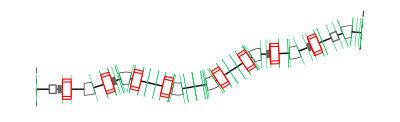

```mathematica
LAT//MADDraw
```

betax, alphax, betay, alphay, dx, dpx

```mathematica
beta0={10.4329,13.1447,13.1042,1.847,0.04066945,0.52648514}
```

{10.4329,13.1447,13.1042,1.847,0.0406695,0.526485}

```mathematica
MADWrite["merge",LAT,Slice->5];
MADStringWrite["merge","INITIAL: beta0, betx = "<>ToString[NumberRight[beta0[[1]]]]<>", bety = "<>ToString[NumberRight[beta0[[3]]]]<>",  &
alfx = "<>ToString[NumberRight[beta0[[2]]]]<>", alfy = "<>ToString[NumberRight[beta0[[4]]]]<>",  &
dx = "<>ToString[NumberRight[beta0[[5]]]]<>", dpx = "<>ToString[NumberRight[beta0[[6]]]]<>",  &
dy = 0, dpy = 0\n"];
MADStringWrite["merge","select,optics,full
optics,filename=optics.txt, BETA0=INITIAL,&
columns=s,name,betx,bety,alfx,alfy,dx,dpx\n"];
RunMAD["merge.mff"];
mfsInterpret["optics.txt"];
```

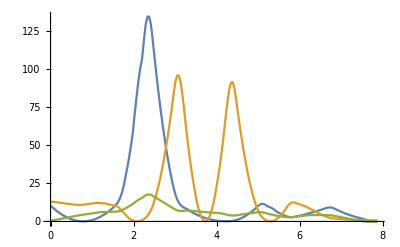

```mathematica
ListLinePlot[{Transpose[{S,BETX}],Transpose[{S,BETY}],Transpose[{S,10 DX}]},PlotRange->All]
```

```mathematica
getTwiss[]:={BETX,ALFX,BETY,ALFY,DX,DPX}[[All,-1]]
```

```mathematica
Unprotect[baseTwiss]
```

{baseTwiss}

```mathematica
baseTwiss=getTwiss[]
Protect[baseTwiss];
```

{0.0795041,0.145028,0.764578,-0.125511,-0.0299682,-0.0593739}

```mathematica
quads=Union[Select[MADFlatten[LAT],#[[2]]==="Quadrupole"&]]
```

{{S1$PIP02$MS1019,Quadrupole,0.2,1.56954,---,---,},{S1$PIP03$MS1020,Quadrupole,0.2,-10.8659,---,---,},{S1$PIP04$MS1022,Quadrupole,0.2,11.0137,---,---,},{S1$PIP05$MS1023,Quadrupole,0.2,-12.6049,---,---,},{S1$PIP08$MS1024,Quadrupole,0.2,-13.0748,---,---,},{S1$PIP09$MS1025,Quadrupole,0.2,10.9554,---,---,},{S1$PIP10$MS1027,Quadrupole,0.00700034,-13.0516,---,---,},{S1$PIP10$MS1028,Quadrupole,0.193,-13.0516,---,---,},{S1$PIP11$MS1030,Quadrupole,0.007,6.65818,---,---,},{S1$PIP11$MS1031,Quadrupole,0.193,6.65818,---,---,}}

```mathematica
startK=#[[4]]&/@quads
```

{1.56954,-10.8659,11.0137,-12.6049,-13.0748,10.9554,-13.0516,-13.0516,6.65818,6.65818}

```mathematica
gradient[data_]:=Block[{k},
k=data[[All,1]];
Coefficient[Fit[Transpose[{k,#}],{1,fitvar},fitvar],fitvar]&/@Rest[Transpose[data]]
]
```

```mathematica
matFunc[quad_,k_]:=Block[{startK},
startK=ToExpression[quad[[1]]][[1,4]];
ToExpression[quad[[1]]<>"[[1,4]]="<>ToString[NumberRight[k]]];
MADWrite["merge",LAT,Slice->5];
MADStringWrite["merge","INITIAL: beta0, betx = "<>ToString[NumberRight[beta0[[1]]]]<>", bety = "<>ToString[NumberRight[beta0[[3]]]]<>",  &
alfx = "<>ToString[NumberRight[beta0[[2]]]]<>", alfy = "<>ToString[NumberRight[beta0[[4]]]]<>",  &
dx = "<>ToString[NumberRight[beta0[[5]]]]<>", dpx = "<>ToString[NumberRight[beta0[[6]]]]<>",  &
dy = 0, dpy = 0\n"];
MADStringWrite["merge","select,optics,full
optics,filename=optics.txt, BETA0=INITIAL,&
columns=s,name,betx,bety,alfx,alfy,dx,dpx\n"];
RunMAD["merge.mff"];
mfsInterpret["optics.txt"];
ToExpression[quad[[1]]<>"[[1,4]]="<>ToString[NumberRight[startK]]];
Join[{k},baseTwiss-getTwiss[]]
]
```

```mathematica
getMatrixData[]:=Block[{quad=#[[1]],startK=#[[2]]},
testdata=matFunc[quad,#+startK]&/@Range[-0.1,0.1,0.1];
gradient[testdata]/baseTwiss]&/@Transpose[{quads,startK}]
```

```mathematica
startK
```

{1.56954,-10.8659,11.0137,-12.6049,-13.0748,10.9554,-13.0516,-13.0516,6.65818,6.65818}

```mathematica
rmdata=getMatrixData[]
```

{{0.043482,0.0869487,-1.48093,11.2978,-0.21099,-1.34914},{1.23367,21.3902,-1.31583,6.70264,5.13327,1.85512},{10.9023,174.368,-0.647939,4.97556,36.5104,16.7366},{1.24705,18.5452,-13.3682,88.4344,5.01233,2.85988},{-0.060217,0.223095,-12.5127,86.2339,-0.375932,1.76759},{-0.668588,13.9353,-0.5426,3.16707,-3.71349,7.05992},{-0.00315078,0.161348,-0.0373801,0.336305,-0.0351706,0.0470493},{-0.0378094,3.88037,-1.41162,12.1334,-0.864149,0.975925},{0.0184267,0.426435,-0.0174345,0.0855702,-0.081136,-0.00362954},{0.553449,11.9215,-0.386193,1.56759,-2.15262,-0.246497}}

```mathematica
testKnobs[knobValues_]:=Block[{},
ToExpression[#[[1]][[1]]<>"[[1,4]]="<>ToString[NumberRight[#[[2]]]]]&/@Transpose[{quads,knobValues}];
MADWrite["merge",LAT,Slice->5];
MADStringWrite["merge","INITIAL: beta0, betx = "<>ToString[NumberRight[beta0[[1]]]]<>", bety = "<>ToString[NumberRight[beta0[[3]]]]<>",  &
alfx = "<>ToString[NumberRight[beta0[[2]]]]<>", alfy = "<>ToString[NumberRight[beta0[[4]]]]<>",  &
dx = "<>ToString[NumberRight[beta0[[5]]]]<>", dpx = "<>ToString[NumberRight[beta0[[6]]]]<>",  &
dy = 0, dpy = 0\n"];
MADStringWrite["merge","select,optics,full
optics,filename=optics.txt, BETA0=INITIAL,&
columns=s,name,betx,bety,alfx,alfy,dx,dpx\n"];
RunMAD["merge.mff"];
mfsInterpret["optics.txt"];
ToExpression[#[[1]][[1]]<>"[[1,4]]="<>ToString[NumberRight[#[[2]]]]]&/@Transpose[{quads,startK}];
baseTwiss-getTwiss[]
]
```

```mathematica
Clear[singularValuesDecompositionInverse];
singularValuesDecompositionInverse[list_,n_:All,αin_:0]:=Block[{α=If[αin===0||αin===0.,10^-12,αin]},
{u,w,v}=SingularValueDecomposition[list,n];
(*winv= SparseArray[{i_, i_}:>1/w[[i,i]],Length[w]];*)
winv=SparseArray[{i_, i_}:>w[[i,i]]^1/(w[[i,i]]^2+α^2),Length[w]];
v.winv.ConjugateTranspose[u]
(*PseudoInverse[list,Tolerance->n]*)
]
```

```mathematica
knob[str_,array_]:=startK+str (Transpose[singularValuesDecompositionInverse[rmdata,5,1]].(array/baseTwiss))
```

```mathematica
#/Max[#]&[knob[1,{1,0,0,0,0,0}]-startK]
```

{0.778882,-0.896947,0.266274,-0.750055,0.623787,-1.1045,0.0299906,1.,0.00212084,0.0269208}

```mathematica
knob[1,{1,0,0,0,0,0}]-startK
```

{0.223381,-0.257241,0.0763665,-0.215113,0.1789,-0.316766,0.00860122,0.286797,0.000608251,0.0077208}

```mathematica
startK
```

{1.56954,-10.8659,11.0137,-12.6049,-13.0748,10.9554,-13.0516,-13.0516,6.65818,6.65818}

```mathematica
knob[1,(Transpose[rmdata].startK)]-startK
```

{1031.36,-840.996,120.34,-715.525,680.077,-214.102,38.3115,1202.53,59.7199,1637.77}

```mathematica
quads[[All,1]]
```

{S1$PIP02$MS1019,S1$PIP03$MS1020,S1$PIP04$MS1022,S1$PIP05$MS1023,S1$PIP08$MS1024,S1$PIP09$MS1025,S1$PIP10$MS1027,S1$PIP10$MS1028,S1$PIP11$MS1030,S1$PIP11$MS1031}

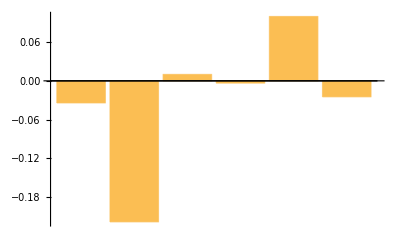

```mathematica
testKnobs[knob[0.1,{0,0,0,0,1,0}]]//BarChart
```